```mathematica
Clear["Global`*"]
```

## Using x1=x1[e1,e2], c=c[e1,e2] rather than the structure of how x1, x2, etc are solved to QSS. First we compute the first order partial derivatives along the QSS surface

```mathematica
F1=e1 f1[x1[e1,e2]]-c[e1,e2];
F2=e2 f2[x1[e1,e2],x2[e1,e2]]-c[e1,e2];
F3=(1-e1-e2) f3[x2[e1,e2]]-c[e1,e2];
derivsNis3=Solve[{
D[F1,e1]==0,
D[F1,e2]==0,
D[F2,e1]==0,
D[F2,e2]==0,
D[F3,e1]==0,
D[F3,e2]==0
},
{Derivative[1,0][x1][e1,e2] ,Derivative[0,1][x1][e1,e2],Derivative[1,0][x2][e1,e2],Derivative[0,1][x2][e1,e2],Derivative[1,0][c][e1,e2],Derivative[0,1][c][e1,e2]}];
rulesfor2ndorder={f1[x1[e1,e2]]->Subscript[f, 1],
f2[x1[e1,e2],x2[e1,e2]]->Subscript[f, 2],
f3[x2[e1,e2]]->Subscript[f, 3],
Derivative[1,0][x1][e1,e2]->dx1de1,
Derivative[0,1][x1][e1,e2]->dx1de2,
Derivative[1,0][x2][e1,e2]->dx2de1,
Derivative[0,1][x2][e1,e2]->dx2de2,
Derivative[1,0][c][e1,e2]->dcde1,
Derivative[0,1][c][e1,e2]->dcde2,
f1'[x1[e1,e2]]->-Subscript[f, 1,2],
Derivative[1,0][f2][x1[e1,e2],x2[e1,e2]]->Subscript[f, 2,1],
Derivative[0,1][f2][x1[e1,e2],x2[e1,e2]]->-Subscript[f, 2,2],
f3'[x2[e1,e2]]->Subscript[f, 3,1]};
enzrules={e1->c/Subscript[f, 1],e2->c/Subscript[f, 2]};
derivsNis3/.rulesfor2ndorder//FullSimplify
derivssimpler=derivsNis3/.rulesfor2ndorder/.enzrules/.{c->1/(1/Subscript[f, 1] + 1/Subscript[f, 2] + 1/Subscript[f, 3])}//FullSimplify
```

{{dx1de1→(-e2 (f_1+f_3) f_(2,2)+(-1+e1+e2) f_1 f_(3,1))/(-e1 e2 f_(1,2) f_(2,2)+(-1+e1+e2) (e1 f_(1,2)+e2 f_(2,1)) f_(3,1)),dx1de2→-(e2 f_3 f_(2,2)+(-1+e1+e2) f_2 f_(3,1))/(-e1 e2 f_(1,2) f_(2,2)+(-1+e1+e2) (e1 f_(1,2)+e2 f_(2,1)) f_(3,1)),dx2de1→-(e1 f_3 f_(1,2)+e2 (f_1+f_3) f_(2,1))/(-e1 e2 f_(1,2) f_(2,2)+(-1+e1+e2) (e1 f_(1,2)+e2 f_(2,1)) f_(3,1)),dx2de2→-(e1 (f_2+f_3) f_(1,2)+e2 f_3 f_(2,1))/(-e1 e2 f_(1,2) f_(2,2)+(-1+e1+e2) (e1 f_(1,2)+e2 f_(2,1)) f_(3,1)),dcde1→(e1 e2 f_3 f_(1,2) f_(2,2)+e2 (-1+e1+e2) f_1 f_(2,1) f_(3,1))/(-e1 e2 f_(1,2) f_(2,2)+(-1+e1+e2) (e1 f_(1,2)+e2 f_(2,1)) f_(3,1)),dcde2→(e1 f_(1,2) (e2 f_3 f_(2,2)+(-1+e1+e2) f_2 f_(3,1)))/(-e1 e2 f_(1,2) f_(2,2)+(-1+e1+e2) (e1 f_(1,2)+e2 f_(2,1)) f_(3,1))}}

{{dx1de1→((f_2 f_3+f_1 (f_2+f_3)) (f_3 (f_1+f_3) f_(2,2)+f_1 f_2 f_(3,1)))/(f_2 f_3 (f_3 f_(1,2) f_(2,2)+(f_2 f_(1,2)+f_1 f_(2,1)) f_(3,1))),dx1de2→-((f_2 f_3+f_1 (f_2+f_3)) (-f_3^2 f_(2,2)+f_2^2 f_(3,1)))/(f_2 f_3 (f_3 f_(1,2) f_(2,2)+(f_2 f_(1,2)+f_1 f_(2,1)) f_(3,1))),dx2de1→((f_2 f_3+f_1 (f_2+f_3)) (f_2 f_3 f_(1,2)+f_1 (f_1+f_3) f_(2,1)))/(f_1 f_2 (f_3 f_(1,2) f_(2,2)+(f_2 f_(1,2)+f_1 f_(2,1)) f_(3,1))),dx2de2→((f_2 f_3+f_1 (f_2+f_3)) (f_2 (f_2+f_3) f_(1,2)+f_1 f_3 f_(2,1)))/(f_1 f_2 (f_3 f_(1,2) f_(2,2)+(f_2 f_(1,2)+f_1 f_(2,1)) f_(3,1))),dcde1→(-f_3^2 f_(1,2) f_(2,2)+f_1^2 f_(2,1) f_(3,1))/(f_3 f_(1,2) f_(2,2)+(f_2 f_(1,2)+f_1 f_(2,1)) f_(3,1)),dcde2→(f_(1,2) (-f_3^2 f_(2,2)+f_2^2 f_(3,1)))/(f_3 f_(1,2) f_(2,2)+(f_2 f_(1,2)+f_1 f_(2,1)) f_(3,1))}}

## Now we compute the second order partial derivatives along the surface. In particular, we want to find d^2 c/dei dej, to compute the Hessian and its determinant

```mathematica
F1=e1 f1[x1[e1,e2]]-c[e1,e2];
F2=e2 f2[x1[e1,e2],x2[e1,e2]]-c[e1,e2];
F3=(1-e1-e2) f3[x2[e1,e2]]-c[e1,e2];
rulesfor2ndorder={f1[x1[e1,e2]]->Subscript[f, 1],
f2[x1[e1,e2],x2[e1,e2]]->Subscript[f, 2],
f3[x2[e1,e2]]->Subscript[f, 3],
Derivative[1,0][x1][e1,e2]->dx1de1,
Derivative[0,1][x1][e1,e2]->dx1de2,
Derivative[1,0][x2][e1,e2]->dx2de1,
Derivative[0,1][x2][e1,e2]->dx2de2,
Derivative[1,0][c][e1,e2]->dcde1,
Derivative[0,1][c][e1,e2]->dcde2,
f1'[x1[e1,e2]]->-Subscript[f, 1,2],
Derivative[1,0][f2][x1[e1,e2],x2[e1,e2]]->Subscript[f, 2,1],
Derivative[0,1][f2][x1[e1,e2],x2[e1,e2]]->-Subscript[f, 2,2],
f3'[x2[e1,e2]]->Subscript[f, 3,1]};
extrarules={
f1''[x1[e1,e2]]-> Subscript[f, 1,2,2],
Derivative[1,1][f2][x1[e1,e2],x2[e1,e2]]->Subscript[f, 2,1,2],
Derivative[0,2][f2][x1[e1,e2],x2[e1,e2]]->Subscript[f, 2,2,2],
Derivative[2,0][f2][x1[e1,e2],x2[e1,e2]]->-Subscript[f, 2,1,1],
f3''[x2[e1,e2]]->-Subscript[f, 3,1,1],

Derivative[2,0][x1][e1,e2]->x120,
Derivative[1,1][x1][e1,e2]->x111,
Derivative[0,2][x1][e1,e2]->x102,

Derivative[2,0][x2][e1,e2]->x220,
Derivative[1,1][x2][e1,e2]->x211,
Derivative[0,2][x2][e1,e2]->x202,

Derivative[1,1][c][e1,e2]->c11,
Derivative[2,0][c][e1,e2]->c20,
Derivative[0,2][c][e1,e2]->c02
};
vars={
x120,x111,x102,
x220,x211,x202,
c11,c20,c02};
impliciteqs2ndorder2={
D[D[F1,e1],e1]==0,
D[D[F1,e1],e2]==0,
D[D[F1,e2],e2]==0,
D[D[F2,e1],e1]==0,
D[D[F2,e1],e2]==0,
D[D[F2,e2],e2]==0,
D[D[F3,e1],e1]==0,
D[D[F3,e1],e2]==0,
D[D[F3,e2],e2]==0
}/.rulesfor2ndorder/.extrarules/.derivssimpler[[1]];
coefs={Coefficient[First[List @@ impliciteqs2ndorder2[[1]]],vars],
Coefficient[First[List @@ impliciteqs2ndorder2[[2]]],vars],
Coefficient[First[List @@ impliciteqs2ndorder2[[3]]],vars],
Coefficient[First[List @@ impliciteqs2ndorder2[[4]]],vars],
Coefficient[First[List @@ impliciteqs2ndorder2[[5]]],vars],
Coefficient[First[List @@ impliciteqs2ndorder2[[6]]],vars],
Coefficient[First[List @@ impliciteqs2ndorder2[[7]]],vars],
Coefficient[First[List @@ impliciteqs2ndorder2[[8]]],vars],
Coefficient[First[List @@ impliciteqs2ndorder2[[9]]],vars]}
coefs/.{e1->c/Subscript[f, 1],e2->c/Subscript[f, 2]}/.{c->1/(1/Subscript[f, 1] + 1/Subscript[f, 2] + 1/Subscript[f, 3])}//MatrixForm//FullSimplify
sol2ndorder=Solve[impliciteqs2ndorder2,vars];
```

{{-e1 f_(1,2),0,0,0,0,0,0,-1,0},{0,-e1 f_(1,2),0,0,0,0,-1,0,0},{0,0,-e1 f_(1,2),0,0,0,0,0,-1},{e2 f_(2,1),0,0,-e2 f_(2,2),0,0,0,-1,0},{0,e2 f_(2,1),0,0,-e2 f_(2,2),0,-1,0,0},{0,0,e2 f_(2,1),0,0,-e2 f_(2,2),0,0,-1},{0,0,0,(1-e1-e2) f_(3,1),0,0,0,-1,0},{0,0,0,0,(1-e1-e2) f_(3,1),0,-1,0,0},{0,0,0,0,0,(1-e1-e2) f_(3,1),0,0,-1}}

(-(f_(1,2))/(1+f_1 (1/f_2+1/f_3)) | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | -(f_(1,2))/(1+f_1 (1/f_2+1/f_3)) | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | -(f_(1,2))/(1+f_1 (1/f_2+1/f_3)) | 0 | 0 | 0 | 0 | 0 | -1
(f_(2,1))/(1+f_2 (1/f_1+1/f_3)) | 0 | 0 | -(f_(2,2))/(1+f_2 (1/f_1+1/f_3)) | 0 | 0 | 0 | -1 | 0
0 | (f_(2,1))/(1+f_2 (1/f_1+1/f_3)) | 0 | 0 | -(f_(2,2))/(1+f_2 (1/f_1+1/f_3)) | 0 | -1 | 0 | 0
0 | 0 | (f_(2,1))/(1+f_2 (1/f_1+1/f_3)) | 0 | 0 | -(f_(2,2))/(1+f_2 (1/f_1+1/f_3)) | 0 | 0 | -1
0 | 0 | 0 | (f_1 f_2 f_(3,1))/(f_2 f_3+f_1 (f_2+f_3)) | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | (f_1 f_2 f_(3,1))/(f_2 f_3+f_1 (f_2+f_3)) | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | (f_1 f_2 f_(3,1))/(f_2 f_3+f_1 (f_2+f_3)) | 0 | 0 | -1)

```mathematica
C02=c02/.sol2ndorder/.{e1->c/Subscript[f, 1],e2->c/Subscript[f, 2]}/.{c->1/(1/Subscript[f, 1] + 1/Subscript[f, 2] + 1/Subscript[f, 3])}//Simplify;
C20=c20/.sol2ndorder/.{e1->c/Subscript[f, 1],e2->c/Subscript[f, 2]}/.{c->1/(1/Subscript[f, 1] + 1/Subscript[f, 2] + 1/Subscript[f, 3])}//Simplify;
C11=c11/.sol2ndorder/.{e1->c/Subscript[f, 1],e2->c/Subscript[f, 2]}/.{c->1/(1/Subscript[f, 1] + 1/Subscript[f, 2] + 1/Subscript[f, 3])}//Simplify;
DD=C02 C20 - C11^2 // FullSimplify
```

{-(((f_2 f_3+f_1 (f_2+f_3))^4 f_(1,2) f_(3,1) (-2 f_(2,2) f_(3,1)^2 (2 f_1 f_(1,2) f_(2,1)^2+f_2 (f_(2,1) (2 f_(1,2)^2-f_1 f_(1,2,2))+f_1 f_(1,2) f_(2,1,1)))+f_3 (-2 f_(1,2)^2 f_(2,1) (f_(3,1) (2 f_(2,2)^2-f_2 f_(2,2,2))+f_2 f_(2,2) f_(3,1,1))+f_1 f_(2,1) f_(1,2,2) (f_(3,1) (2 f_(2,2)^2-f_2 f_(2,2,2))+f_2 f_(2,2) f_(3,1,1))+f_1 f_(1,2) (f_(3,1) (-2 f_(2,2)^2 f_(2,1,1)+4 f_(2,1) f_(2,2) f_(2,1,2)+f_2 f_(2,1,2)^2+(2 f_(2,1)^2+f_2 f_(2,1,1)) f_(2,2,2))-f_(2,2) (2 f_(2,1)^2+f_2 f_(2,1,1)) f_(3,1,1)))))/(f_1 f_2 f_3 (f_3 f_(1,2) f_(2,2)+(f_2 f_(1,2)+f_1 f_(2,1)) f_(3,1))^4))}

## So det( Hessian ) is not overly complicated (less so than the individual 2nd order derivatives). How about if we use the explicit form of the fj’s?

```mathematica
explrules = {
Subscript[f, 1]->(x-Subscript[K, 1] y)/(Subscript[a, 1] x+Subscript[b, 1] y + Subscript[c, 1]),
Subscript[f, 2]->(y-Subscript[K, 2] z)/(Subscript[a, 2] y+Subscript[b, 2] z + Subscript[c, 2]),
Subscript[f, 3]->z/(Subscript[a, 3] z+Subscript[c, 3] ),
Subscript[f, 1,2]-> -D[(x-Subscript[K, 1] y)/(Subscript[a, 1] x+Subscript[b, 1] y + Subscript[c, 1]),y]//Simplify,
Subscript[f, 2,1] -> D[(y-Subscript[K, 1] z)/(Subscript[a, 2] y+Subscript[b, 2] z + Subscript[c, 2]),y]//Simplify,
Subscript[f, 2,2] -> -D[(y-Subscript[K, 1] z)/(Subscript[a, 2] y+Subscript[b, 2] z + Subscript[c, 2]),z]//Simplify,
Subscript[f, 3,1] -> D[(z)/(Subscript[a, 3] z+Subscript[c, 3] ),z]//Simplify,
Subscript[f, 1,2,2]->D[D[(x-Subscript[K, 1] y)/(Subscript[a, 1] x+Subscript[b, 1] y + Subscript[c, 1]),y],y]//Simplify,
Subscript[f, 2,1,1]->-D[D[(y-Subscript[K, 1] z)/(Subscript[a, 2] y+Subscript[b, 2] z + Subscript[c, 2]),y],y]//Simplify,
Subscript[f, 2,1,2]->D[D[(y-Subscript[K, 1] z)/(Subscript[a, 2] y+Subscript[b, 2] z + Subscript[c, 2]),y],z]//FullSimplify,
Subscript[f, 2,2,2]->D[D[(y-Subscript[K, 1] z)/(Subscript[a, 2] y+Subscript[b, 2] z + Subscript[c, 2]),z],z]//Simplify,
Subscript[f, 3,1,1]->-D[D[(z)/(Subscript[a, 3] z+Subscript[c, 3] ),z],z]//Simplify
}
DD2=DD/.explrules;
```

{f_1→(x-y K_1)/(x a_1+y b_1+c_1),f_2→(y-z K_2)/(y a_2+z b_2+c_2),f_3→z/(z a_3+c_3),f_(1,2)→(x b_1+(x a_1+c_1) K_1)/(x a_1+y b_1+c_1)^2,f_(2,1)→(z b_2+c_2+z a_2 K_1)/(y a_2+z b_2+c_2)^2,f_(2,2)→(y b_2+(y a_2+c_2) K_1)/(y a_2+z b_2+c_2)^2,f_(3,1)→c_3/(z a_3+c_3)^2,f_(1,2,2)→(2 b_1 (x b_1+(x a_1+c_1) K_1))/(x a_1+y b_1+c_1)^3,f_(2,1,1)→(2 a_2 (z b_2+c_2+z a_2 K_1))/(y a_2+z b_2+c_2)^3,f_(2,1,2)→(-b_2 (-y a_2+z b_2+c_2)+a_2 (y a_2-z b_2+c_2) K_1)/(y a_2+z b_2+c_2)^3,f_(2,2,2)→(2 b_2 (y b_2+(y a_2+c_2) K_1))/(y a_2+z b_2+c_2)^3,f_(3,1,1)→(2 a_3 c_3)/(z a_3+c_3)^3}

```mathematica
DDH={1/((Subscript[a, 3]+z Subscript[b, 3])^4 (Subscript[a, 1]+x Subscript[b, 1]+y Subscript[c, 1])^4 (Subscript[a, 2]+y Subscript[b, 2]+z Subscript[c, 2])^6)Subscript[a, 3]^2 (x Subscript[c, 1]+(Subscript[a, 1]+x Subscript[b, 1]) Subscript[K, 1])^2 ((z (y-z Subscript[K, 1]))/((Subscript[a, 3]+z Subscript[b, 3]) (Subscript[a, 2]+y Subscript[b, 2]+z Subscript[c, 2]))+((x-y Subscript[K, 1]) (z/(Subscript[a, 3]+z Subscript[b, 3])+(y-z Subscript[K, 1])/(Subscript[a, 2]+y Subscript[b, 2]+z Subscript[c, 2])))/(Subscript[a, 1]+x Subscript[b, 1]+y Subscript[c, 1]))^4 (-4 z (Subscript[a, 3]+z Subscript[b, 3]) (Subscript[a, 1]+x Subscript[b, 1]+y Subscript[c, 1]) (x-y Subscript[K, 1]) (y Subscript[c, 2]+(Subscript[a, 2]+y Subscript[b, 2]) Subscript[K, 1])^2 (Subscript[a, 2]+z (Subscript[c, 2]+Subscript[b, 2] Subscript[K, 1]))^2-4 (y-z Subscript[K, 1]) (Subscript[a, 3] (Subscript[a, 1]+x Subscript[b, 1]+y Subscript[c, 1]) (Subscript[a, 2]+y Subscript[b, 2]+z Subscript[c, 2]) (x-y Subscript[K, 1]) (y Subscript[c, 2]+(Subscript[a, 2]+y Subscript[b, 2]) Subscript[K, 1]) (Subscript[a, 2]+z (Subscript[c, 2]+Subscript[b, 2] Subscript[K, 1]))^2-z ((Subscript[a, 3]+z Subscript[b, 3]) Subscript[c, 1] (Subscript[a, 2]+y Subscript[b, 2]+z Subscript[c, 2]) (x-y Subscript[K, 1]) (y Subscript[c, 2]+(Subscript[a, 2]+y Subscript[b, 2]) Subscript[K, 1])^2 (Subscript[a, 2]+z (Subscript[c, 2]+Subscript[b, 2] Subscript[K, 1]))-(Subscript[a, 3]+z Subscript[b, 3]) (Subscript[a, 2]+y Subscript[b, 2]+z Subscript[c, 2]) (x Subscript[c, 1]+(Subscript[a, 1]+x Subscript[b, 1]) Subscript[K, 1]) (y Subscript[c, 2]+(Subscript[a, 2]+y Subscript[b, 2]) Subscript[K, 1])^2 (Subscript[a, 2]+z (Subscript[c, 2]+Subscript[b, 2] Subscript[K, 1]))+(Subscript[a, 1]+x Subscript[b, 1]+y Subscript[c, 1]) (x-y Subscript[K, 1]) (Subscript[b, 3] (Subscript[a, 2]+y Subscript[b, 2]+z Subscript[c, 2]) (y Subscript[c, 2]+(Subscript[a, 2]+y Subscript[b, 2]) Subscript[K, 1]) (Subscript[a, 2]+z (Subscript[c, 2]+Subscript[b, 2] Subscript[K, 1]))^2-(Subscript[a, 3]+z Subscript[b, 3]) Subscript[c, 2] (Subscript[a, 2]+z (Subscript[c, 2]+Subscript[b, 2] Subscript[K, 1]))^2 (y Subscript[c, 2]+(Subscript[a, 2]+y Subscript[b, 2]) Subscript[K, 2])+Subscript[b, 2] (Subscript[a, 3]+z Subscript[b, 3]) (y Subscript[c, 2]+(Subscript[a, 2]+y Subscript[b, 2]) Subscript[K, 1])^2 (Subscript[a, 2]+z (Subscript[c, 2]+Subscript[b, 2] Subscript[K, 2])))))+(y-z Subscript[K, 1])^2 (4 Subscript[c, 1] (Subscript[a, 2]+y Subscript[b, 2]+z Subscript[c, 2]) (x-y Subscript[K, 1]) (Subscript[a, 2]+z (Subscript[c, 2]+Subscript[b, 2] Subscript[K, 1])) ((Subscript[a, 3]-z Subscript[b, 3]) (Subscript[a, 2]+y Subscript[b, 2]+z Subscript[c, 2]) (y Subscript[c, 2]+(Subscript[a, 2]+y Subscript[b, 2]) Subscript[K, 1])+z (Subscript[a, 3]+z Subscript[b, 3]) Subscript[c, 2] (y Subscript[c, 2]+(Subscript[a, 2]+y Subscript[b, 2]) Subscript[K, 2]))-4 (Subscript[a, 2]+y Subscript[b, 2]+z Subscript[c, 2]) (x Subscript[c, 1]+(Subscript[a, 1]+x Subscript[b, 1]) Subscript[K, 1]) (Subscript[a, 2]+z (Subscript[c, 2]+Subscript[b, 2] Subscript[K, 1])) ((Subscript[a, 3]-z Subscript[b, 3]) (Subscript[a, 2]+y Subscript[b, 2]+z Subscript[c, 2]) (y Subscript[c, 2]+(Subscript[a, 2]+y Subscript[b, 2]) Subscript[K, 1])+z (Subscript[a, 3]+z Subscript[b, 3]) Subscript[c, 2] (y Subscript[c, 2]+(Subscript[a, 2]+y Subscript[b, 2]) Subscript[K, 2]))+(Subscript[a, 1]+x Subscript[b, 1]+y Subscript[c, 1]) (x-y Subscript[K, 1]) (4 Subscript[b, 2] (Subscript[a, 3]-z Subscript[b, 3]) (Subscript[a, 2]+y Subscript[b, 2]+z Subscript[c, 2]) (y Subscript[c, 2]+(Subscript[a, 2]+y Subscript[b, 2]) Subscript[K, 1]) (Subscript[a, 2]+z (Subscript[c, 2]+Subscript[b, 2] Subscript[K, 2]))+z (Subscript[a, 3]+z Subscript[b, 3]) (4 Subscript[b, 2] Subscript[c, 2] (y Subscript[c, 2]+(Subscript[a, 2]+y Subscript[b, 2]) Subscript[K, 2]) (Subscript[a, 2]+z (Subscript[c, 2]+Subscript[b, 2] Subscript[K, 2]))-(Subscript[a, 2] (-Subscript[c, 2]+Subscript[b, 2] Subscript[K, 2])+(y Subscript[b, 2]-z Subscript[c, 2]) (Subscript[c, 2]+Subscript[b, 2] Subscript[K, 2]))^2))))};
DDH/.{Subscript[a, 1]->1,Subscript[b, 1]->1,Subscript[c, 1]->0,Subscript[k, 2]->1,Subscript[a, 2]->1,Subscript[b, 2]->0,Subscript[c, 2]->0,Subscript[a, 3]->1,Subscript[b, 3]->0,x->Subscript[x, 0],y->Subscript[x, 1],z->Subscript[x, 2]}//Factor
```

{(4 K_1^3 x_1 (-x_0+K_1^2 x_2) (x_0 x_1-K_1 x_1^2+x_0 x_2-K_1 x_0 x_2+x_1 x_2-K_1 x_1 x_2+K_1^2 x_1 x_2+x_0 x_1 x_2-K_1 x_2^2-K_1 x_0 x_2^2)^4)/(1+x_0)^5}

```mathematica
DDnum=Numerator[DD2/.{y->Subscript[K, 2] z + t,x->Subscript[K, 1] y+s}]/.{t->0,s->0}
```

{a_3^2 (y c_1 K_1+K_1 (a_1+y b_1 K_1))^2 ((z (-z K_1+z K_2))/((a_3+z b_3) (a_2+z c_2+z b_2 K_2))+((y K_1-z K_1 K_2) (z/(a_3+z b_3)+(-z K_1+z K_2)/(a_2+z c_2+z b_2 K_2)))/(a_1+y b_1 K_1+z c_1 K_2))^4 (-4 z (a_3+z b_3) (a_2+z (c_2+b_2 K_1))^2 (a_1+y b_1 K_1+z c_1 K_2) (y K_1-z K_1 K_2) (z c_2 K_2+K_1 (a_2+z b_2 K_2))^2-4 (-z K_1+z K_2) (a_3 (a_2+z (c_2+b_2 K_1))^2 (a_2+z c_2+z b_2 K_2) (a_1+y b_1 K_1+z c_1 K_2) (y K_1-z K_1 K_2) (z c_2 K_2+K_1 (a_2+z b_2 K_2))-z (-(a_3+z b_3) (y c_1 K_1+K_1 (a_1+y b_1 K_1)) (a_2+z (c_2+b_2 K_1)) (a_2+z c_2+z b_2 K_2) (z c_2 K_2+K_1 (a_2+z b_2 K_2))^2+(a_3+z b_3) c_1 (a_2+z (c_2+b_2 K_1)) (a_2+z c_2+z b_2 K_2) (y K_1-z K_1 K_2) (z c_2 K_2+K_1 (a_2+z b_2 K_2))^2+(a_1+y b_1 K_1+z c_1 K_2) (y K_1-z K_1 K_2) (b_3 (a_2+z (c_2+b_2 K_1))^2 (a_2+z c_2+z b_2 K_2) (z c_2 K_2+K_1 (a_2+z b_2 K_2))+b_2 (a_3+z b_3) (a_2+z (c_2+b_2 K_2)) (z c_2 K_2+K_1 (a_2+z b_2 K_2))^2-(a_3+z b_3) c_2 (a_2+z (c_2+b_2 K_1))^2 (z c_2 K_2+K_2 (a_2+z b_2 K_2)))))+(-z K_1+z K_2)^2 (-4 (y c_1 K_1+K_1 (a_1+y b_1 K_1)) (a_2+z (c_2+b_2 K_1)) (a_2+z c_2+z b_2 K_2) ((a_3-z b_3) (a_2+z c_2+z b_2 K_2) (z c_2 K_2+K_1 (a_2+z b_2 K_2))+z (a_3+z b_3) c_2 (z c_2 K_2+K_2 (a_2+z b_2 K_2)))+4 c_1 (a_2+z (c_2+b_2 K_1)) (a_2+z c_2+z b_2 K_2) (y K_1-z K_1 K_2) ((a_3-z b_3) (a_2+z c_2+z b_2 K_2) (z c_2 K_2+K_1 (a_2+z b_2 K_2))+z (a_3+z b_3) c_2 (z c_2 K_2+K_2 (a_2+z b_2 K_2)))+(a_1+y b_1 K_1+z c_1 K_2) (y K_1-z K_1 K_2) (4 b_2 (a_3-z b_3) (a_2+z c_2+z b_2 K_2) (a_2+z (c_2+b_2 K_2)) (z c_2 K_2+K_1 (a_2+z b_2 K_2))+z (a_3+z b_3) (4 b_2 c_2 (a_2+z (c_2+b_2 K_2)) (z c_2 K_2+K_2 (a_2+z b_2 K_2))-(a_2 (-c_2+b_2 K_2)+(c_2+b_2 K_2) (-z c_2+z b_2 K_2))^2))))}

## To make the argument for global stability work using level sets, we need information about xi_0’(t). So we must treat the DAE as an ODE by implicit differentiation, to find xi0’(t).

```mathematica
Obj=1/(1/f1[Subscript[y, 0],Subscript[y, 1]]+1/f2[Subscript[y, 1],Subscript[y, 2]]+1/f3[Subscript[y, 2]]);
G1=D[Obj,Subscript[y, 1]];
G2=D[Obj,Subscript[y, 2]];
eqsopt={G1,G2};
M={{D[eqsopt[[1]],Subscript[y, 0]],D[eqsopt[[1]],Subscript[y, 1]],D[eqsopt[[1]],Subscript[y, 2]]},{D[eqsopt[[2]],Subscript[y, 0]],D[eqsopt[[2]],Subscript[y, 1]],D[eqsopt[[2]],Subscript[y, 2]]},{0,1,0}};
sol=LinearSolve[M,{0,0,Subscript[x, 1]}];
rules={f1[Subscript[y, 0],Subscript[y, 1]]->Subscript[f, 1],f2[Subscript[y, 1],Subscript[y, 2]]->Subscript[f, 2],f3[Subscript[y, 2]]->Subscript[f, 3],
Derivative[1,0][f1][Subscript[y, 0],Subscript[y, 1]] ->Subscript[f, 1,1,0],
Derivative[0,1][f1][Subscript[y, 0],Subscript[y, 1]] ->-Subscript[f, 1,0,1],
Derivative[1,1][f1][Subscript[y, 0],Subscript[y, 1]] ->Subscript[f, 1,1,1],
Derivative[0,2][f1][Subscript[y, 0],Subscript[y, 1]] ->Subscript[f, 1,0,2],

Derivative[1,0][f2][Subscript[y, 1],Subscript[y, 2]]->Subscript[f, 2,1,0],
Derivative[0,1][f2][Subscript[y, 1],Subscript[y, 2]]->-Subscript[f, 2,0,1],
Derivative[1,1][f2][Subscript[y, 1],Subscript[y, 2]]->Subscript[f, 2,1,1],
Derivative[0,2][f2][Subscript[y, 1],Subscript[y, 2]]->Subscript[f, 2,0,2],
Derivative[2,0][f2][Subscript[y, 1],Subscript[y, 2]]->-Subscript[f, 2,2,0],

f3'[Subscript[y, 2]]->Subscript[f, 3,1],
f3''[Subscript[y, 2]]->-Subscript[f, 3,2]};
sol[[1]]/.rules//FullSimplify
```

-((x_1 (-f_2^4 (2 f_(3,1)^2+f_3 f_(3,2)) (2 f_(1,0,1)^2-f_1 f_(1,0,2))+f_2^5 (-2 f_(3,2) f_(1,0,1)^2+(2 f_(3,1)^2+(f_1+f_3) f_(3,2)) f_(1,0,2))+f_1^2 f_3^2 (2 f_1 f_(2,0,2) f_(2,1,0)^2+2 f_3 f_(2,0,2) f_(2,1,0)^2+4 f_1 f_(2,0,1) f_(2,1,0) f_(2,1,1)+4 f_3 f_(2,0,1) f_(2,1,0) f_(2,1,1)+f_1 f_3 f_(2,1,1)^2+(-2 (f_1+f_3) f_(2,0,1)^2+f_1 f_3 f_(2,0,2)) f_(2,2,0))+f_2^3 (-f_3^3 f_(1,0,2) f_(2,0,2)+f_3^2 (2 f_(1,0,1)^2-f_1 f_(1,0,2)) f_(2,0,2)+f_1 (-8 f_(3,1)^2 f_(1,0,1) f_(2,1,0)-f_1 (2 f_(3,1)^2+f_1 f_(3,2)) f_(2,2,0))-f_3 (4 f_(3,1) ((2 f_(1,0,1)^2-f_1 f_(1,0,2)) f_(2,0,1)+f_1 f_(1,0,1) f_(2,1,1))+f_1 f_(3,2) (4 f_(1,0,1) f_(2,1,0)+f_1 f_(2,2,0))))+f_2^2 (2 f_3^2 (-2 f_(1,0,1)^2+f_1 f_(1,0,2)) f_(2,0,1)^2+f_3^3 (2 f_(1,0,1)^2 f_(2,0,2)+f_(1,0,2) (2 f_(2,0,1)^2-f_1 f_(2,0,2)))-2 f_1^2 (2 f_(3,1)^2+f_1 f_(3,2)) f_(2,1,0)^2-2 f_1^3 f_(3,1)^2 f_(2,2,0)-f_1 f_3 (8 f_(3,1) f_(1,0,1) f_(2,0,1) f_(2,1,0)+f_1 f_(3,2) (2 f_(2,1,0)^2+f_1 f_(2,2,0))))+f_1 f_2 f_3 (4 f_1^2 f_(3,1) (f_(2,1,0) f_(2,1,1)-f_(2,0,1) f_(2,2,0))+f_1^2 f_3 (f_(2,1,1)^2+f_(2,0,2) f_(2,2,0))+f_3^2 (4 f_(1,0,1) (f_(2,0,2) f_(2,1,0)+f_(2,0,1) f_(2,1,1))+f_1 (f_(2,1,1)^2+f_(2,0,2) f_(2,2,0))))))/(f_2 (f_2^3 (2 f_(3,1)^2+f_3 f_(3,2)) (2 f_(1,0,1) f_(1,1,0)+f_1 f_(1,1,1))+f_2^4 (2 f_(3,2) f_(1,0,1) f_(1,1,0)+(2 f_(3,1)^2+(f_1+f_3) f_(3,2)) f_(1,1,1))+f_2 f_3 (f_3 (2 (2 f_(1,0,1) f_(1,1,0)+(f_1+f_3) f_(1,1,1)) f_(2,0,1)^2-f_3 (2 f_(1,0,1) f_(1,1,0)+f_1 f_(1,1,1)) f_(2,0,2))+4 f_1 f_(3,1) f_(1,1,0) f_(2,0,1) f_(2,1,0))-2 f_1 f_3^3 f_(1,1,0) (f_(2,0,2) f_(2,1,0)+f_(2,0,1) f_(2,1,1))+f_2^2 (-f_3^3 f_(1,1,1) f_(2,0,2)-f_3^2 (2 f_(1,0,1) f_(1,1,0)+f_1 f_(1,1,1)) f_(2,0,2)+4 f_1 f_(3,1)^2 f_(1,1,0) f_(2,1,0)+2 f_3 (f_1 f_(3,2) f_(1,1,0) f_(2,1,0)+f_(3,1) (2 (2 f_(1,0,1) f_(1,1,0)+f_1 f_(1,1,1)) f_(2,0,1)+f_1 f_(1,1,0) f_(2,1,1)))))))

```mathematica
F=(x-Ky)/(a + b x + c y)
D[D[F,x],x]//Simplify
D[D[F,x],y]//Simplify
D[D[F,y],y]//Simplify
```

(-Ky+x)/(a+b x+c y)

-(2 b (a+b Ky+c y))/(a+b x+c y)^3

-(c (a+2 b Ky-b x+c y))/(a+b x+c y)^3

(2 c^2 (-Ky+x))/(a+b x+c y)^3

```mathematica
M={{Subscript[L, 11],Subscript[L, 12],Subscript[L, 13]},{Subscript[L, 21],Subscript[L, 22],Subscript[L, 23]},{0,1,0}};
sol=LinearSolve[M,{0,0,Subscript[x, 1]}];
sol[[1]]
```

-((-L_13 L_22+L_12 L_23) x_1)/(-L_13 L_21+L_11 L_23)

```mathematica
M/.rules//FullSimplify//MatrixForm
```

((f_2 f_3^2 (f_2 (2 (f_2+f_3) f_(1,0,1) f_(1,1,0)+(f_2 f_3+f_1 (f_2+f_3)) f_(1,1,1))+2 f_1 f_3 f_(1,1,0) f_(2,1,0)))/(f_2 f_3+f_1 (f_2+f_3))^3 | (2 ((f_(1,0,1))/f_1^2-(f_(2,1,0))/f_2^2)^2-(1/f_1+1/f_2+1/f_3) ((2 f_(1,0,1)^2-f_1 f_(1,0,2))/f_1^3+(2 f_(2,1,0)^2+f_2 f_(2,2,0))/f_2^3))/(1/f_1+1/f_2+1/f_3)^3 | (2 (-(f_(3,1))/f_3^2+(f_(2,0,1))/f_2^2) ((f_(1,0,1))/f_1^2-(f_(2,1,0))/f_2^2)+((1/f_1+1/f_2+1/f_3) (2 f_(2,0,1) f_(2,1,0)+f_2 f_(2,1,1)))/f_2^3)/(1/f_1+1/f_2+1/f_3)^3
-(2 f_(1,1,0) (-(f_(3,1))/f_3^2+(f_(2,0,1))/f_2^2))/(f_1^2 (1/f_1+1/f_2+1/f_3)^3) | (2 (-(f_(3,1))/f_3^2+(f_(2,0,1))/f_2^2) ((f_(1,0,1))/f_1^2-(f_(2,1,0))/f_2^2)+((1/f_1+1/f_2+1/f_3) (2 f_(2,0,1) f_(2,1,0)+f_2 f_(2,1,1)))/f_2^3)/(1/f_1+1/f_2+1/f_3)^3 | (2 ((f_(3,1))/f_3^2-(f_(2,0,1))/f_2^2)^2-(1/f_1+1/f_2+1/f_3) ((2 f_(3,1)^2+f_3 f_(3,2))/f_3^3+(2 f_(2,0,1)^2-f_2 f_(2,0,2))/f_2^3))/(1/f_1+1/f_2+1/f_3)^3
0 | 1 | 0)

```mathematica
F1=Subscript[e, 1] Subscript[f, 1][Subscript[x, 0],Subscript[x, 1][Subscript[x, 0]]]-c[Subscript[x, 0]];
F2=Subscript[e, 2] Subscript[f, 2][Subscript[x, 1][Subscript[x, 0]],Subscript[x, 2][Subscript[x, 0]]]-c[Subscript[x, 0]];
F3=(1-Subscript[e, 1]-Subscript[e, 2])Subscript[f, 3][Subscript[x, 2][Subscript[x, 0]]]-c[Subscript[x, 0]];
eqsc={D[F1,Subscript[x, 0]]==0,D[F2,Subscript[x, 0]]==0,D[F3,Subscript[x, 0]]==0};
solsc=Solve[eqsc,{Subscript[x, 1]'[Subscript[x, 0]],Subscript[x, 2]'[Subscript[x, 0]],c'[Subscript[x, 0]]}];
rules={ 
Derivative[0,1][Subscript[f, 1]][Subscript[x, 0],Subscript[x, 1][Subscript[x, 0]]]->-Subscript[f, 1,2], 
Derivative[1,0][Subscript[f, 1]][Subscript[x, 0],Subscript[x, 1][Subscript[x, 0]]]->Subscript[f, 1,1],
Derivative[1,0][Subscript[f, 2]][Subscript[x, 1][Subscript[x, 0]],Subscript[x, 2][Subscript[x, 0]]]->Subscript[f, 2,1],
 Derivative[0,1][Subscript[f, 2]][Subscript[x, 1][Subscript[x, 0]],Subscript[x, 2][Subscript[x, 0]]]->-Subscript[f, 2,2],
Subscript[f, 3]'[Subscript[x, 2][Subscript[x, 0]]]->Subscript[f, 3,1] 
};
c'[Subscript[x, 0]]/.solsc/.rules//FullSimplify
```

{(e_1 e_2 (-1+e_1+e_2) f_(1,1) f_(2,1) f_(3,1))/(-e_1 e_2 f_(1,2) f_(2,2)+(-1+e_1+e_2) (e_1 f_(1,2)+e_2 f_(2,1)) f_(3,1))}

## How about showing concavity of c(e1,e2) by taking a straight line from two sets of enzyme concentrations with equal flux value and showing that the flux along the way increases and then decreases?

```mathematica
erules={e1->a1(1-t) + t b1, e2->(1-t) a2 + t b2,e3->(1-t) a3 + t b3};
frules={
f1[x1[e1[t],e2[t]]]->Subscript[f, 1],
f2[x1[e1[t],e2[t]],x2[e1[t],e2[t]]]->Subscript[f, 2],
f3[x2[e1[t],e2[t]]]->Subscript[f, 3],
f1'[x1[e1[t],e2[t]]]->Subscript[f, 1,2],
Derivative[1,0][f2][x1[e1[t],e2[t]],x2[e1[t],e2[t]]]->Subscript[f, 2,1],
Derivative[0,1][f2][x1[e1[t],e2[t]],x2[e1[t],e2[t]]]->Subscript[f, 2,2],
f3'[x2[e1[t],e2[t]]]->Subscript[f, 3,1],
Derivative[1,0][x1][e1[t],e2[t]]->Subscript[x, 1,e1],
Derivative[0,1][x1][e1[t],e2[t]]->Subscript[x, 1,e2],
Derivative[1,0][x2][e1[t],e2[t]]->Subscript[x, 2,e1],
Derivative[0,1][x2][e1[t],e2[t]]->Subscript[x, 2,e2],
e1[t]->Subscript[e, 1],
e2[t]->Subscript[e, 2]
};
F1=e1[t]f1[x1[e1[t],e2[t]]]-c[t];
F2=e2 [t]f2[x1[e1[t],e2[t]],x2[e1[t],e2[t]]]-c[t];
F3=(1-e1[t]-e2[t]) f3[x2[e1[t],e2[t]]]-c[t];
ddteqs={
F1==0,F2==0,F3==0,
D[F1,t]==0,D[F2,t]==0,D[F3,t]==0
};
vars={Derivative[1,0][x1][e1[t],e2[t]],
Derivative[0,1][x1][e1[t],e2[t]],
Derivative[1,0][x2][e1[t],e2[t]],
Derivative[0,1][x2][e1[t],e2[t]],c'[t]};
M = {
Coefficient[First[List @@ ddteqs[[1]]],vars],
Coefficient[First[List @@ ddteqs[[2]]],vars],
Coefficient[First[List @@ ddteqs[[3]]],vars],
Coefficient[First[List @@ ddteqs[[4]]],vars],
Coefficient[First[List @@ ddteqs[[5]]],vars],
Coefficient[First[List @@ ddteqs[[6]]],vars]
}/.frules//MatrixForm
ddteqs[[4]]
```

(0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
e_1 f_(1,2) e1'[t] | e_1 f_(1,2) e2'[t] | 0 | 0 | -1
e_2 f_(2,1) e1'[t] | e_2 f_(2,1) e2'[t] | e_2 f_(2,2) e1'[t] | e_2 f_(2,2) e2'[t] | -1
0 | 0 | f_(3,1) e1'[t]-e_1 f_(3,1) e1'[t]-e_2 f_(3,1) e1'[t] | f_(3,1) e2'[t]-e_1 f_(3,1) e2'[t]-e_2 f_(3,1) e2'[t] | -1)

-c'[t]+f1[x1[e1[t],e2[t]]] e1'[t]+e1[t] f1'[x1[e1[t],e2[t]]] (e2'[t] x1^(0,1)[e1[t],e2[t]]+e1'[t] x1^(1,0)[e1[t],e2[t]])==0

```mathematica
rulesNis3notenz0={
f1[x1[e1,e2]]->Subscript[f, 1],
f2[x1[e1,e2],x2[e1,e2]]->Subscript[f, 2],
f3[x2[e1,e2]]->Subscript[f, 3],
Derivative[1,0][x1][e1,e2]->dx1de1,
Derivative[0,1][x1][e1,e2]->dx1de2,
Derivative[1,0][x2][e1,e2]->dx2de3,
Derivative[0,1][x2][e1,e2]->dx2dc,
Derivative[1,0][c][e1,e2]->dcde1,
Derivative[0,1][c][e1,e2]->dcde2,
f1'[x1[e1,e2]]->-Subscript[f, 1,2],
Derivative[1,0][f2][x1[e1,e2],x2[e1,e2]]->Subscript[f, 2,1],
Derivative[0,1][f2][x1[e1,e2],x2[e1,e2]]->-Subscript[f, 2,2],
f3'[x2[e1,e2]]->Subscript[f, 3,1]};
rulesNis3notenz1={
f1[x1[e1,e2]]->Subscript[g, 1],
f2[x1[e1,e2],x2[e1,e2]]->Subscript[g, 2],
f3[x2[e1,e2]]->Subscript[g, 3],
Derivative[1,0][x1][e1,e2]->dx1de1,
Derivative[0,1][x1][e1,e2]->dx1de2,
Derivative[1,0][x2][e1,e2]->dx2de3,
Derivative[0,1][x2][e1,e2]->dx2dc,
Derivative[1,0][c][e1,e2]->dcde1,
Derivative[0,1][c][e1,e2]->dcde2,
f1'[x1[e1,e2]]->-Subscript[g, 1,2],
Derivative[1,0][f2][x1[e1,e2],x2[e1,e2]]->Subscript[g, 2,1],
Derivative[0,1][f2][x1[e1,e2],x2[e1,e2]]->-Subscript[g, 2,2],
f3'[x2[e1,e2]]->Subscript[g, 3,1]};
derivsfort0=derivsNis3/.rulesNis3notenz0
derivsfort1=derivsNis3/.rulesNis3notenz1
```

{{dx1de1→-(-e2 f_1 f_(2,2)-e2 f_3 f_(2,2)-f_1 f_(3,1)+e1 f_1 f_(3,1)+e2 f_1 f_(3,1))/(e1 e2 f_(1,2) f_(2,2)+e1 f_(1,2) f_(3,1)-e1^2 f_(1,2) f_(3,1)-e1 e2 f_(1,2) f_(3,1)+e2 f_(2,1) f_(3,1)-e1 e2 f_(2,1) f_(3,1)-e2^2 f_(2,1) f_(3,1)),dx1de2→f_3/(e1 f_(1,2))-((e1 f_2 f_(1,2)+f_3 (e1 f_(1,2)+e2 f_(2,1))) (-f_(3,1)+e1 f_(3,1)+e2 f_(3,1)))/(e1 f_(1,2) (-e1 e2 f_(1,2) f_(2,2)-(1-e1-e2) (e1 f_(1,2)+e2 f_(2,1)) f_(3,1))),dx2de3→-(e2 f_1 f_(2,1)+f_3 (e1 f_(1,2)+e2 f_(2,1)))/(-e1 e2 f_(1,2) f_(2,2)-(1-e1-e2) (e1 f_(1,2)+e2 f_(2,1)) f_(3,1)),dx2dc→-(e1 f_2 f_(1,2)+f_3 (e1 f_(1,2)+e2 f_(2,1)))/(-e1 e2 f_(1,2) f_(2,2)-(1-e1-e2) (e1 f_(1,2)+e2 f_(2,1)) f_(3,1)),dcde1→-(e1 e2 f_3 f_(1,2) f_(2,2)-e2 f_1 f_(2,1) f_(3,1)+e1 e2 f_1 f_(2,1) f_(3,1)+e2^2 f_1 f_(2,1) f_(3,1))/(e1 e2 f_(1,2) f_(2,2)+e1 f_(1,2) f_(3,1)-e1^2 f_(1,2) f_(3,1)-e1 e2 f_(1,2) f_(3,1)+e2 f_(2,1) f_(3,1)-e1 e2 f_(2,1) f_(3,1)-e2^2 f_(2,1) f_(3,1)),dcde2→-f_3+((e1 f_2 f_(1,2)+f_3 (e1 f_(1,2)+e2 f_(2,1))) (-f_(3,1)+e1 f_(3,1)+e2 f_(3,1)))/(-e1 e2 f_(1,2) f_(2,2)-(1-e1-e2) (e1 f_(1,2)+e2 f_(2,1)) f_(3,1))}}

{{dx1de1→-(-e2 g_1 g_(2,2)-e2 g_3 g_(2,2)-g_1 g_(3,1)+e1 g_1 g_(3,1)+e2 g_1 g_(3,1))/(e1 e2 g_(1,2) g_(2,2)+e1 g_(1,2) g_(3,1)-e1^2 g_(1,2) g_(3,1)-e1 e2 g_(1,2) g_(3,1)+e2 g_(2,1) g_(3,1)-e1 e2 g_(2,1) g_(3,1)-e2^2 g_(2,1) g_(3,1)),dx1de2→g_3/(e1 g_(1,2))-((e1 g_2 g_(1,2)+g_3 (e1 g_(1,2)+e2 g_(2,1))) (-g_(3,1)+e1 g_(3,1)+e2 g_(3,1)))/(e1 g_(1,2) (-e1 e2 g_(1,2) g_(2,2)-(1-e1-e2) (e1 g_(1,2)+e2 g_(2,1)) g_(3,1))),dx2de3→-(e2 g_1 g_(2,1)+g_3 (e1 g_(1,2)+e2 g_(2,1)))/(-e1 e2 g_(1,2) g_(2,2)-(1-e1-e2) (e1 g_(1,2)+e2 g_(2,1)) g_(3,1)),dx2dc→-(e1 g_2 g_(1,2)+g_3 (e1 g_(1,2)+e2 g_(2,1)))/(-e1 e2 g_(1,2) g_(2,2)-(1-e1-e2) (e1 g_(1,2)+e2 g_(2,1)) g_(3,1)),dcde1→-(e1 e2 g_3 g_(1,2) g_(2,2)-e2 g_1 g_(2,1) g_(3,1)+e1 e2 g_1 g_(2,1) g_(3,1)+e2^2 g_1 g_(2,1) g_(3,1))/(e1 e2 g_(1,2) g_(2,2)+e1 g_(1,2) g_(3,1)-e1^2 g_(1,2) g_(3,1)-e1 e2 g_(1,2) g_(3,1)+e2 g_(2,1) g_(3,1)-e1 e2 g_(2,1) g_(3,1)-e2^2 g_(2,1) g_(3,1)),dcde2→-g_3+((e1 g_2 g_(1,2)+g_3 (e1 g_(1,2)+e2 g_(2,1))) (-g_(3,1)+e1 g_(3,1)+e2 g_(3,1)))/(-e1 e2 g_(1,2) g_(2,2)-(1-e1-e2) (e1 g_(1,2)+e2 g_(2,1)) g_(3,1))}}

```mathematica
de1dt=b1-a1; de2dt=b2-a2;
dcdt00=(dcde1 de1dt+dcde2 de2dt)/.derivsfort0[[1]]/.{e1->Subscript[a, 1],e2->Subscript[a, 2]}//FullSimplify
dcdt10=(dcde1 de1dt+dcde2 de2dt)/.derivsfort1[[1]]/.{e1->Subscript[b, 1],e2->Subscript[b, 2]}//FullSimplify
dcdt0=(dcde1 de1dt+dcde2 de2dt)/.derivsfort0[[1]]/.{e1->c/Subscript[f, 1],e2->c/Subscript[f, 2],a1->c/Subscript[f, 1],a2->c/Subscript[f, 2],b1->c/Subscript[g, 1],b2->c/Subscript[g, 2]}//FullSimplify
dcdt1=(dcde1 de1dt+dcde2 de2dt)/.derivsfort1[[1]]/.{e1->c/Subscript[g, 1],e2->c/Subscript[g, 2],a1->c/Subscript[f, 1],a2->c/Subscript[f, 2],b1->c/Subscript[g, 1],b2->c/Subscript[g, 2]}//FullSimplify
dcdt0==dcdt1 //FullSimplify
```

((-a1-a2+b1+b2) a_1 a_2 f_3 f_(1,2) f_(2,2)-(-1+a_1+a_2) ((a2-b2) a_1 f_2 f_(1,2)+(a1-b1) a_2 f_1 f_(2,1)) f_(3,1))/(-a_1 a_2 f_(1,2) f_(2,2)+(-1+a_1+a_2) (a_1 f_(1,2)+a_2 f_(2,1)) f_(3,1))

((-a1-a2+b1+b2) b_1 b_2 g_3 g_(1,2) g_(2,2)-(-1+b_1+b_2) ((a2-b2) b_1 g_2 g_(1,2)+(a1-b1) b_2 g_1 g_(2,1)) g_(3,1))/(-b_1 b_2 g_(1,2) g_(2,2)+(-1+b_1+b_2) (b_1 g_(1,2)+b_2 g_(2,1)) g_(3,1))

(c (c f_3 (f_1 f_2 g_1+(f_1 f_2-(f_1+f_2) g_1) g_2) f_(1,2) f_(2,2)+(f_1 (c-f_2)+c f_2) (f_2 g_1 (f_2-g_2) f_(1,2)+f_1 (f_1-g_1) g_2 f_(2,1)) f_(3,1)))/(g_1 g_2 (-c f_1 f_2 f_(1,2) f_(2,2)+(f_1 (c-f_2)+c f_2) (f_2 f_(1,2)+f_1 f_(2,1)) f_(3,1)))

(c (c (f_1 f_2 g_1+(f_1 f_2-(f_1+f_2) g_1) g_2) g_3 g_(1,2) g_(2,2)+(g_1 (c-g_2)+c g_2) (f_1 (f_2-g_2) g_2 g_(1,2)+f_2 (f_1-g_1) g_1 g_(2,1)) g_(3,1)))/(f_1 f_2 (-c g_1 g_2 g_(1,2) g_(2,2)+(g_1 (c-g_2)+c g_2) (g_2 g_(1,2)+g_1 g_(2,1)) g_(3,1)))

(c (c f_3 (f_1 f_2 g_1+(f_1 f_2-(f_1+f_2) g_1) g_2) f_(1,2) f_(2,2)+(f_1 (c-f_2)+c f_2) (f_2 g_1 (f_2-g_2) f_(1,2)+f_1 (f_1-g_1) g_2 f_(2,1)) f_(3,1)))/(g_1 g_2 (-c f_1 f_2 f_(1,2) f_(2,2)+(f_1 (c-f_2)+c f_2) (f_2 f_(1,2)+f_1 f_(2,1)) f_(3,1)))==(c (c (f_1 f_2 g_1+(f_1 f_2-(f_1+f_2) g_1) g_2) g_3 g_(1,2) g_(2,2)+(g_1 (c-g_2)+c g_2) (f_1 (f_2-g_2) g_2 g_(1,2)+f_2 (f_1-g_1) g_1 g_(2,1)) g_(3,1)))/(f_1 f_2 (-c g_1 g_2 g_(1,2) g_(2,2)+(g_1 (c-g_2)+c g_2) (g_2 g_(1,2)+g_1 g_(2,1)) g_(3,1)))

```mathematica
D[(x-K y)/(a + b x + c y),x]//Simplify
D[(x-K y)/(a + b x + c y),y]//Simplify
```

(a+(c+b K) y)/(a+b x+c y)^2

```mathematica
frules = {f1->(x0-K1 x1)/(a1 + b1 x0 + c1 x1), f2->(x1-K2 x2)/(a2 + b2 x1 + c2 x2),f3->(x2)/(a3 + b3 x2 )};
Obj = 1/f1 + 1/f2 + 1/f3 /. frules;
opteqs = {D[Obj,x1]==0,D[Obj,x2]==0}//FullSimplify
x0sol=Solve[opteqs[[1]],{x0}];
x2sol=Solve[opteqs[[2]],{x2}];
sols = {x0/.{x0sol[[2]]},x2/.x2sol[[2]]}/.x2sol[[2]]//FullSimplify
```

{(a1 K1+(c1+b1 K1) x0)/(x0-K1 x1)^2==(a2+(c2+b2 K2) x2)/(x1-K2 x2)^2,(a2 K2+(c2+b2 K2) x1)/(x1-K2 x2)^2==a3/x2^2}

{{((c2 x1+K2 (a2-a3 K2+b2 x1)) (-2 a2 K1 x1-c1 x1^2-b1 K1 x1^2+(2 c2 K1 x1 (a3 K2 x1-√(a3 x1^2 (a2 K2+c2 x1+b2 K2 x1))))/(c2 x1+K2 (a2-a3 K2+b2 x1))+(2 b2 K1 K2 x1 (a3 K2 x1-√(a3 x1^2 (a2 K2+c2 x1+b2 K2 x1))))/(c2 x1+K2 (a2-a3 K2+b2 x1))+(2 c1 K2 x1 (-a3 K2 x1+√(a3 x1^2 (a2 K2+(c2+b2 K2) x1))))/(c2 x1+K2 (a2-a3 K2+b2 x1))+(2 b1 K1 K2 x1 (-a3 K2 x1+√(a3 x1^2 (a2 K2+(c2+b2 K2) x1))))/(c2 x1+K2 (a2-a3 K2+b2 x1))-(c1 K2^2 (-a3 K2 x1+√(a3 x1^2 (a2 K2+(c2+b2 K2) x1)))^2)/(c2 x1+K2 (a2-a3 K2+b2 x1))^2-(b1 K1 K2^2 (-a3 K2 x1+√(a3 x1^2 (a2 K2+(c2+b2 K2) x1)))^2)/(c2 x1+K2 (a2-a3 K2+b2 x1))^2+√((2 a2 K1 x1+c1 x1^2+b1 K1 x1^2+(2 c2 K1 x1 (-a3 K2 x1+√(a3 x1^2 (a2 K2+(c2+b2 K2) x1))))/(c2 x1+K2 (a2-a3 K2+b2 x1))-(2 c1 K2 x1 (-a3 K2 x1+√(a3 x1^2 (a2 K2+(c2+b2 K2) x1))))/(c2 x1+K2 (a2-a3 K2+b2 x1))-(2 b1 K1 K2 x1 (-a3 K2 x1+√(a3 x1^2 (a2 K2+(c2+b2 K2) x1))))/(c2 x1+K2 (a2-a3 K2+b2 x1))+(2 b2 K1 K2 x1 (-a3 K2 x1+√(a3 x1^2 (a2 K2+(c2+b2 K2) x1))))/(c2 x1+K2 (a2-a3 K2+b2 x1))+(c1 K2^2 (-a3 K2 x1+√(a3 x1^2 (a2 K2+(c2+b2 K2) x1)))^2)/(c2 x1+K2 (a2-a3 K2+b2 x1))^2+(b1 K1 K2^2 (-a3 K2 x1+√(a3 x1^2 (a2 K2+(c2+b2 K2) x1)))^2)/(c2 x1+K2 (a2-a3 K2+b2 x1))^2)^2-1/(c2 x1+K2 (a2-a3 K2+b2 x1))^3 4 K1 x1 (-a2^2 K2+a2 a3 K2^2-a2 (c2+b2 K2) x1+(c2+b2 K2) (a3 K2 x1-√(a3 x1^2 (a2 K2+c2 x1+b2 K2 x1)))) (a1 (a2 K2+(c2+b2 K2) x1) (K2 (a2+a3 K2) x1+(c2+b2 K2) x1^2-2 K2 √(a3 x1^2 (a2 K2+c2 x1+b2 K2 x1)))-K1 x1 (c2 x1+K2 (a2-a3 K2+b2 x1)) (a2^2 K2-a2 a3 K2^2+a2 (c2+b2 K2) x1+(c2+b2 K2) (-a3 K2 x1+√(a3 x1^2 (a2 K2+(c2+b2 K2) x1))))))))/(2 (-a2^2 K2+a2 a3 K2^2-a2 (c2+b2 K2) x1+(c2+b2 K2) (a3 K2 x1-√(a3 x1^2 (a2 K2+c2 x1+b2 K2 x1)))))},(a3 x1^2)/(a3 K2 x1+√(a3 x1^2 (a2 K2+(c2+b2 K2) x1)))}

```mathematica
x0sol[[2]]//FullSimplify
x1sol=Solve[x2==(x2/.x2sol[[2]]),x1];
x1sol[[2]]
Series[x1/.x1sol[[2]],{x2,1,2}]
Series[x2/.x2sol[[2]],{x1,1,2}];
```

{x0→1/(2 (a2+(c2+b2 K2) x2))((c1+b1 K1) x1^2+(c1+b1 K1) K2^2 x2^2+2 x1 (a2 K1+c2 K1 x2-(c1+(b1-b2) K1) K2 x2)-√((x1-K2 x2)^2 (4 a1 K1 (a2+(c2+b2 K2) x2)+(c1+b1 K1) (4 a2 K1 x1+4 K1 (c2+b2 K2) x1 x2+c1 (x1-K2 x2)^2+b1 K1 (x1-K2 x2)^2))))}

{x1→(2 a3 K2 x2+c2 x2^2+b2 K2 x2^2+√(4 a3 K2 (a2-a3 K2) x2^2+x2^2 (-2 a3 K2-c2 x2-b2 K2 x2)^2))/(2 a3)}

(c2+2 a3 K2+b2 K2+√(c2^2+4 a2 a3 K2+4 a3 c2 K2+2 b2 c2 K2+4 a3 b2 K2^2+b2^2 K2^2))/(2 a3)+((2 c2+2 a3 K2+2 b2 K2+(2 (c2^2+2 a2 a3 K2+3 a3 c2 K2+2 b2 c2 K2+3 a3 b2 K2^2+b2^2 K2^2))/(√(c2^2+4 a2 a3 K2+4 a3 c2 K2+2 b2 c2 K2+4 a3 b2 K2^2+b2^2 K2^2))) (x2-1))/(2 a3)+1/(2 a3)(c2+b2 K2+1/2 √(c2^2+4 a2 a3 K2+4 a3 c2 K2+2 b2 c2 K2+4 a3 b2 K2^2+b2^2 K2^2) (-(4 (c2^2+2 a2 a3 K2+3 a3 c2 K2+2 b2 c2 K2+3 a3 b2 K2^2+b2^2 K2^2)^2)/((4 a3 K2 (a2-a3 K2)+(-c2-2 a3 K2-b2 K2)^2)^2)+(2 (3 c2^2+2 a2 a3 K2+6 a3 c2 K2+6 b2 c2 K2+6 a3 b2 K2^2+3 b2^2 K2^2))/(4 a3 K2 (a2-a3 K2)+(-c2-2 a3 K2-b2 K2)^2))) (x2-1)^2+O[x2-1]^3

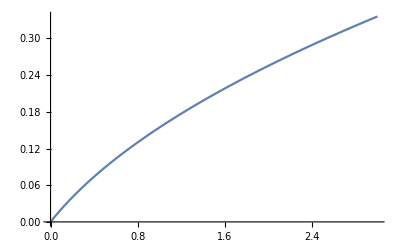

-Graphics-

```mathematica
Plot[x1^2/(2 x1+√(x1^2 (3 2+(4+5 2) x1))),{x1,0,3}]
Plot[x1/(2 +√(3 2+(4+5 2) x1)),{x1,0,3}]
```

$Aborted

{b2+b3+(a2+a3 K2)/x1+(a1+b1 x0+c1 x1)/(x0-K1 x1)+(2 √(a3 x1^2 (a2 K2+c2 x1+b2 K2 x1)))/x1^2}

{-b2-(a2+a3 K2)/x1-(2 √(a3 x1^2 (a2 K2+c2 x1+b2 K2 x1)))/x1^2+a3/x2+(a2+b2 x1+c2 x2)/(x1-K2 x2)}

{-23+4/x2+(3+3 x2)/(1-2 x2)}

{3/(1-2 x2)-4/x2^2+(2 (3+3 x2))/(1-2 x2)^2}

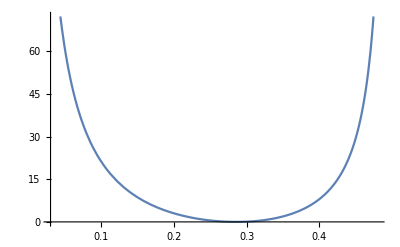

```mathematica
Obj1 = Obj//FullSimplify
Obj2=Obj/.{x2sol[[2]]}//FullSimplify
Obj1-Obj2//FullSimplify
Objdiff=(Obj1-Obj2)/.{a2->2,a3->4,b2->1,b3->5,c2->3,c3->6,K2->2,K3->1,x1->1}
Plot[Objdiff,{x2,0.03,0.48}]
```

```mathematica
solx2d=Solve[(Obj1-Obj2)==0,x2]
(Obj1-Obj2)/.solx2d[[2]]//Simplify
```

{{x2→(a3 K2 x1^2+x1 √(a3 x1^2 (a2 K2+c2 x1+b2 K2 x1))-√(-a2 a3 K2 x1^4-a3 c2 x1^5-a3 b2 K2 x1^5+a3 x1^4 (a2 K2+c2 x1+b2 K2 x1)))/(a2 K2 x1+a3 K2^2 x1+c2 x1^2+b2 K2 x1^2+2 K2 √(a3 x1^2 (a2 K2+c2 x1+b2 K2 x1)))},{x2→(a3 K2 x1^2+x1 √(a3 x1^2 (a2 K2+c2 x1+b2 K2 x1))+√(-a2 a3 K2 x1^4-a3 c2 x1^5-a3 b2 K2 x1^5+a3 x1^4 (a2 K2+c2 x1+b2 K2 x1)))/(a2 K2 x1+a3 K2^2 x1+c2 x1^2+b2 K2 x1^2+2 K2 √(a3 x1^2 (a2 K2+c2 x1+b2 K2 x1)))}}

{0}

# How far can we get by choosing kinetics such that the QSSA is explicitly solvable for x in terms of e?

## In this example, we use nearly trivial kinetics, but with a bit of saturation in f_1. We can find the QSSA map from e to x and c

```mathematica
Subscript[ff, 1]=(Subscript[x, 0]- Subscript[k, 1] Subscript[x, 1])/(1+Subscript[x, 0]);
Subscript[ff, 2]=(Subscript[x, 1]- Subscript[x, 2]);
Subscript[ff, 3]=Subscript[x, 2];
sols=Solve[{Subscript[e, 1] Subscript[ff, 1]==c,Subscript[e, 2] Subscript[ff, 2]==c,(1-Subscript[e, 1]-Subscript[e, 2])Subscript[ff, 3]==c},{Subscript[x, 1],Subscript[x, 2],c}]//Simplify;
x1sol=sols[[1]][[1]]
csol=sols[[1]][[3]]
```

x_1→((-1+e_1) e_1 x_0)/((-1+e_1) e_1 k_1+(-1+e_1) e_2 (1+x_0)+e_2^2 (1+x_0))

c→(e_1 e_2 (-1+e_1+e_2) x_0)/((-1+e_1) e_1 k_1+(-1+e_1) e_2 (1+x_0)+e_2^2 (1+x_0))

## Now compute the epsilons. First the optimum compute xi_0 and xi_2 in terms of x_1.

```mathematica
Opt=1/Subscript[ff, 1] + 1/Subscript[ff, 2] + 1/Subscript[ff, 3];
Opteqs = {D[Opt,Subscript[x, 1]]==0,D[Opt,Subscript[x, 2]]==0}
x02=Solve[Opteqs,{Subscript[x, 0],Subscript[x, 2]}][[2]]
```

{(k_1 (1+x_0))/(x_0-k_1 x_1)^2-1/(x_1-x_2)^2==0,1/(x_1-x_2)^2-1/x_2^2==0}

{x_0→1/8 (8 k_1 x_1+k_1 x_1^2+√k_1 x_1 √(16+16 k_1 x_1+k_1 x_1^2)),x_2→x_1/2}

## Then compute epsilon_1 and epsilon_2., first in terms of x_1 and then in terms of e_1 and e_2 using the QSSA map.

```mathematica
eps1=1/Subscript[ff, 1]/Opt /. x02//FullSimplify
eps2=1/Subscript[ff, 2]/Opt /. x02//FullSimplify
eps1e=Simplify[eps1/.x1sol,Assumptions->{Subscript[k, 1]>0, x0>0,Subscript[e, 1] > 0, Subscript[e, 2] > 0, Subscript[e, 1]+ Subscript[e, 2] <1}]
eps2e=Simplify[eps2/.x1sol,Assumptions->{Subscript[k, 1]>0, x0>0,Subscript[e, 1] > 0, Subscript[e, 2] > 0, Subscript[e, 1]+ Subscript[e, 2] <1}]
```

(-2-k_1 x_1+√k_1 √(16+k_1 x_1 (16+x_1)))/(-2+8 k_1)

(4 √k_1)/(√k_1 (8+x_1)+√(16+k_1 x_1 (16+x_1)))

(-2-((-1+e_1) e_1 k_1 x_0)/((-1+e_1) e_1 k_1+(-1+e_1) e_2 (1+x_0)+e_2^2 (1+x_0))+√(k_1 (16+((-1+e_1) e_1 k_1 x_0 (16 (-1+e_1) e_2 (1+x_0)+16 e_2^2 (1+x_0)+(-1+e_1) e_1 (16 k_1+x_0)))/(((-1+e_1) e_1 k_1+(-1+e_1) e_2 (1+x_0)+e_2^2 (1+x_0))^2))))/(-2+8 k_1)

(4 √k_1)/(√k_1 (8+((-1+e_1) e_1 x_0)/((-1+e_1) e_1 k_1+(-1+e_1) e_2 (1+x_0)+e_2^2 (1+x_0)))+√(16+((-1+e_1) e_1 k_1 x_0 (16 (-1+e_1) e_2 (1+x_0)+16 e_2^2 (1+x_0)+(-1+e_1) e_1 (16 k_1+x_0)))/(((-1+e_1) e_1 k_1+(-1+e_1) e_2 (1+x_0)+e_2^2 (1+x_0))^2)))

## Check: there is nontrivial adaptive control: eps_1actually depends on x_1. The second plot is x_1 as a function of e_1 and e_2.

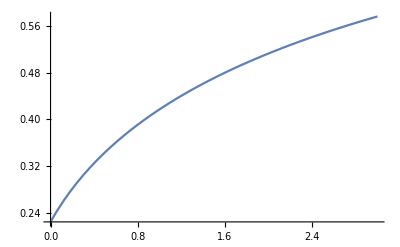

-Graphics3D-

1.83673

```mathematica
Plot[{eps1}/.{Subscript[k, 1]->3,Subscript[x, 0]->10},{Subscript[x, 1],0,3}]
Plot3D[Re[Subscript[x, 1]/.x1sol/.{Subscript[k, 1]->3,Subscript[x, 0]->10}],{Subscript[e, 1],0,1},{Subscript[e, 2],0,1},
	RegionFunction->Function[{x,y,z},x+y≤1],
	ViewPoint->Top,
	ColorFunction->Function[{x,y,z},Hue[z]]]
Re[Subscript[x, 1]/.x1sol/.{Subscript[k, 1]->3,Subscript[x, 0]->10,Subscript[e, 1]->1/2,Subscript[e, 2]->1/3}]//N
```

## stst flux en predicted stst flux are ordered. Stst flux < Predicted flux, unless e = eopt

```mathematica
cc=csol/.{Subscript[k, 1]->3,Subscript[x, 0]->10}
cpred=csol/.{Subscript[e, 1]->eps1e,Subscript[e, 2]->eps2e};
ccpred = cpred/.{Subscript[k, 1]->3,Subscript[x, 0]->10};
Plot3D[{(c/.ccpred)-(c/.cc),0},{Subscript[e, 1],0,1},{Subscript[e, 2],0,1},
	RegionFunction->Function[{x,y,z},x+y≤1],
	ColorFunction->Function[{x,y,z},Hue[z]]]
```

c→(10 e_1 e_2 (-1+e_1+e_2))/(3 (-1+e_1) e_1+11 (-1+e_1) e_2+11 e_2^2)

-Graphics3D-

## Don’t redo the following. It will take ages.

```mathematica
ccpred//FullSimplify
```

c→1/1199 10 (-23+(1635 (-1+e_1) e_1)/(3 (-1+e_1) e_1+11 (-1+e_1) e_2+11 e_2^2)-(21615 (-1+e_1) e_1)/(27 (-1+e_1) e_1+109 (-1+e_1) e_2+109 e_2^2)+6 √(48+(180 (-1+e_1) e_1 (29 (-1+e_1) e_1+88 (-1+e_1) e_2+88 e_2^2))/((3 (-1+e_1) e_1+11 (-1+e_1) e_2+11 e_2^2)^2))-(165 e_1 √(48+(180 (-1+e_1) e_1 (29 (-1+e_1) e_1+88 (-1+e_1) e_2+88 e_2^2))/((3 (-1+e_1) e_1+11 (-1+e_1) e_2+11 e_2^2)^2)))/(27 (-1+e_1) e_1+109 (-1+e_1) e_2+109 e_2^2)+(165 e_1^2 √(48+(180 (-1+e_1) e_1 (29 (-1+e_1) e_1+88 (-1+e_1) e_2+88 e_2^2))/((3 (-1+e_1) e_1+11 (-1+e_1) e_2+11 e_2^2)^2)))/(27 (-1+e_1) e_1+109 (-1+e_1) e_2+109 e_2^2))

## So I’ve set it apart not to lose it.

```mathematica
Cpred={c->1/1199 10 (-23+(1635 (-1+Subscript[e, 1]) Subscript[e, 1])/(3 (-1+Subscript[e, 1]) Subscript[e, 1]+11 (-1+Subscript[e, 1]) Subscript[e, 2]+11 Subscript[e, 2]^2)-(21615 (-1+Subscript[e, 1]) Subscript[e, 1])/(27 (-1+Subscript[e, 1]) Subscript[e, 1]+109 (-1+Subscript[e, 1]) Subscript[e, 2]+109 Subscript[e, 2]^2)+6 √(48+(180 (-1+Subscript[e, 1]) Subscript[e, 1] (29 (-1+Subscript[e, 1]) Subscript[e, 1]+88 (-1+Subscript[e, 1]) Subscript[e, 2]+88 Subscript[e, 2]^2))/((3 (-1+Subscript[e, 1]) Subscript[e, 1]+11 (-1+Subscript[e, 1]) Subscript[e, 2]+11 Subscript[e, 2]^2)^2))-(165 Subscript[e, 1] √(48+(180 (-1+Subscript[e, 1]) Subscript[e, 1] (29 (-1+Subscript[e, 1]) Subscript[e, 1]+88 (-1+Subscript[e, 1]) Subscript[e, 2]+88 Subscript[e, 2]^2))/((3 (-1+Subscript[e, 1]) Subscript[e, 1]+11 (-1+Subscript[e, 1]) Subscript[e, 2]+11 Subscript[e, 2]^2)^2)))/(27 (-1+Subscript[e, 1]) Subscript[e, 1]+109 (-1+Subscript[e, 1]) Subscript[e, 2]+109 Subscript[e, 2]^2)+(165 Subscript[e, 1]^2 √(48+(180 (-1+Subscript[e, 1]) Subscript[e, 1] (29 (-1+Subscript[e, 1]) Subscript[e, 1]+88 (-1+Subscript[e, 1]) Subscript[e, 2]+88 Subscript[e, 2]^2))/((3 (-1+Subscript[e, 1]) Subscript[e, 1]+11 (-1+Subscript[e, 1]) Subscript[e, 2]+11 Subscript[e, 2]^2)^2)))/(27 (-1+Subscript[e, 1]) Subscript[e, 1]+109 (-1+Subscript[e, 1]) Subscript[e, 2]+109 Subscript[e, 2]^2))};
```

```mathematica
sols[[1]]
Opt/.{sols[[1]][[1]],sols[[1]][[2]]};
Subscript[eta, 1]=sols[[1]][[1]]/.{Subscript[e, 1]->eps1e,Subscript[e, 2]->eps2e};
Subscript[eta, 2]=sols[[1]][[2]]/.{Subscript[e, 1]->eps1e,Subscript[e, 2]->eps2e};
Opteta=Opt/.{Subscript[eta, 1],Subscript[eta, 2]};
Opt-Opteta;
```

sols⟦1⟧

## This is det(Hessian) of c(e_1,e_2), using the explicit kinetics. det(Hessian) is negative definite if we choose the kinetics parameter of the above example.

```mathematica
params={x->Subscript[x, 0],y->Subscript[x, 1],z->Subscript[x, 2]};
detHes=DD2/.params//Factor
denom = detHes//Denominator;
numer=detHes//Numerator;
```

{(c_3^2 (c_1 K_1+b_1 x_0+a_1 K_1 x_0)^2 (c_3 x_0 x_1-c_3 K_1 x_1^2+c_2 x_0 x_2-c_3 K_2 x_0 x_2+c_1 x_1 x_2-c_2 K_1 x_1 x_2+c_3 K_1 K_2 x_1 x_2+a_1 x_0 x_1 x_2+a_2 x_0 x_1 x_2+a_3 x_0 x_1 x_2+b_1 x_1^2 x_2-a_2 K_1 x_1^2 x_2-a_3 K_1 x_1^2 x_2-c_1 K_2 x_2^2+b_2 x_0 x_2^2-a_1 K_2 x_0 x_2^2-a_3 K_2 x_0 x_2^2-b_2 K_1 x_1 x_2^2-b_1 K_2 x_1 x_2^2+a_3 K_1 K_2 x_1 x_2^2)^4 (4 c_2^3 K_1 x_0+4 b_2 c_2^2 x_0 x_1+8 a_2 c_2^2 K_1 x_0 x_1+4 a_2 b_2 c_2 x_0 x_1^2+4 a_2^2 c_2 K_1 x_0 x_1^2+4 c_2^3 K_1^3 x_2-4 c_2^3 K_1^2 K_2 x_2+8 b_2 c_2^2 K_1 x_0 x_2+8 a_2 c_2^2 K_1^2 x_0 x_2-4 a_2 c_2^2 K_1 K_2 x_0 x_2+4 b_2 c_2^2 K_1^2 x_1 x_2+4 a_2 c_2^2 K_1^3 x_1 x_2-4 b_2 c_2^2 K_1 K_2 x_1 x_2-4 a_2 c_2^2 K_1^2 K_2 x_1 x_2+7 b_2^2 c_2 x_0 x_1 x_2+18 a_2 b_2 c_2 K_1 x_0 x_1 x_2+11 a_2^2 c_2 K_1^2 x_0 x_1 x_2-4 a_2 b_2 c_2 K_2 x_0 x_1 x_2-4 a_2^2 c_2 K_1 K_2 x_0 x_1 x_2+b_2^2 c_2 K_1 x_1^2 x_2+2 a_2 b_2 c_2 K_1^2 x_1^2 x_2+a_2^2 c_2 K_1^3 x_1^2 x_2+3 a_2 b_2^2 x_0 x_1^2 x_2+6 a_2^2 b_2 K_1 x_0 x_1^2 x_2+3 a_2^3 K_1^2 x_0 x_1^2 x_2+a_2 b_2^2 K_1 x_1^3 x_2+2 a_2^2 b_2 K_1^2 x_1^3 x_2+a_2^3 K_1^3 x_1^3 x_2+4 b_2 c_2^2 K_1^3 x_2^2+4 a_2 c_2^2 K_1^4 x_2^2-4 b_2 c_2^2 K_1^2 K_2 x_2^2-4 a_2 c_2^2 K_1^3 K_2 x_2^2+4 b_2^2 c_2 K_1 x_0 x_2^2+8 a_2 b_2 c_2 K_1^2 x_0 x_2^2+4 a_2^2 c_2 K_1^3 x_0 x_2^2+b_2^2 c_2 K_2 x_0 x_2^2-2 a_2 b_2 c_2 K_1 K_2 x_0 x_2^2-3 a_2^2 c_2 K_1^2 K_2 x_0 x_2^2+4 b_2^2 c_2 K_1^2 x_1 x_2^2+8 a_2 b_2 c_2 K_1^3 x_1 x_2^2+4 a_2^2 c_2 K_1^4 x_1 x_2^2-5 b_2^2 c_2 K_1 K_2 x_1 x_2^2-10 a_2 b_2 c_2 K_1^2 K_2 x_1 x_2^2-5 a_2^2 c_2 K_1^3 K_2 x_1 x_2^2+3 b_2^3 x_0 x_1 x_2^2+10 a_2 b_2^2 K_1 x_0 x_1 x_2^2+11 a_2^2 b_2 K_1^2 x_0 x_1 x_2^2+4 a_2^3 K_1^3 x_0 x_1 x_2^2-3 a_2 b_2^2 K_2 x_0 x_1 x_2^2-6 a_2^2 b_2 K_1 K_2 x_0 x_1 x_2^2-3 a_2^3 K_1^2 K_2 x_0 x_1 x_2^2+b_2^3 K_1 x_1^2 x_2^2+2 a_2 b_2^2 K_1^2 x_1^2 x_2^2+a_2^2 b_2 K_1^3 x_1^2 x_2^2-a_2 b_2^2 K_1 K_2 x_1^2 x_2^2-2 a_2^2 b_2 K_1^2 K_2 x_1^2 x_2^2-a_2^3 K_1^3 K_2 x_1^2 x_2^2+b_2^3 K_2 x_0 x_2^3+2 a_2 b_2^2 K_1 K_2 x_0 x_2^3+a_2^2 b_2 K_1^2 K_2 x_0 x_2^3-b_2^3 K_1 K_2 x_1 x_2^3-2 a_2 b_2^2 K_1^2 K_2 x_1 x_2^3-a_2^2 b_2 K_1^3 K_2 x_1 x_2^3))/((x_0-K_1 x_1) x_2 (c_2+a_2 x_1+b_2 x_2) (x_1-K_2 x_2) (c_1 c_2 c_3 x_0+a_1 c_2 c_3 x_0^2+2 b_1 c_2 c_3 x_0 x_1+a_2 c_1 c_3 K_1 x_1^2-b_1 c_2 c_3 K_1 x_1^2+a_2 b_1 c_3 x_0 x_1^2+a_1 a_2 c_3 K_1 x_0 x_1^2+c_1 c_2 c_3 K_1^2 x_2-c_1 c_2 c_3 K_1 K_2 x_2+b_2 c_1 c_3 x_0 x_2+a_2 c_1 c_3 K_1 x_0 x_2+b_1 c_2 c_3 K_1 x_0 x_2+a_1 c_2 c_3 K_1^2 x_0 x_2-b_1 c_2 c_3 K_2 x_0 x_2-a_1 c_2 c_3 K_1 K_2 x_0 x_2+a_1 b_2 c_3 x_0^2 x_2+a_1 a_2 c_3 K_1 x_0^2 x_2+b_2 c_1 c_3 K_1 x_1 x_2-a_2 c_1 c_3 K_1 K_2 x_1 x_2+3 b_1 b_2 c_3 x_0 x_1 x_2+2 a_2 b_1 c_3 K_1 x_0 x_1 x_2+a_1 b_2 c_3 K_1 x_0 x_1 x_2-a_2 b_1 c_3 K_2 x_0 x_1 x_2-a_1 a_2 c_3 K_1 K_2 x_0 x_1 x_2-b_1 b_2 c_3 K_1 x_1^2 x_2-a_2 b_1 c_3 K_1^2 x_1^2 x_2+a_3 c_1 c_2 K_1^2 x_2^2-b_2 c_1 c_3 K_1 K_2 x_2^2+a_3 b_1 c_2 K_1 x_0 x_2^2+a_1 a_3 c_2 K_1^2 x_0 x_2^2-b_1 b_2 c_3 K_2 x_0 x_2^2-a_1 b_2 c_3 K_1 K_2 x_0 x_2^2+a_3 b_2 c_1 K_1 x_1 x_2^2+a_2 a_3 c_1 K_1^2 x_1 x_2^2+a_3 b_1 b_2 x_0 x_1 x_2^2+a_2 a_3 b_1 K_1 x_0 x_1 x_2^2+a_1 a_3 b_2 K_1 x_0 x_1 x_2^2+a_1 a_2 a_3 K_1^2 x_0 x_1 x_2^2)^4)}

```mathematica
denomsquarefree=denom[[1]]//FactorSquareFreeList;
denomterms={};
For[i=2,i<=Length[denomsquarefree],i++,If[OddQ[denomsquarefree[[i]][[2]]],denomterms=Append[denomterms,denomsquarefree[[i]][[1]]]]]

numersquarefree=numer[[1]]//FactorSquareFreeList;
numerterms={};
For[i=2,i<=Length[numersquarefree],i++,If[OddQ[numersquarefree[[i]][[2]]],numerterms=Append[numerterms,numersquarefree[[i]][[1]]]]]

detHesSquarefree=(Times@@numerterms)/Times@@denomterms ;
detHesSquarefreeST=(Times@@numerterms)/Times@@denomterms /.{Subscript[x, 0]->Subscript[K, 1] Subscript[x, 1]+s}/.{Subscript[x, 1]->Subscript[K, 2] Subscript[x, 2] + t}//Factor//FullSimplify
```

((c_2+b_2 x_2) (4 c_2^2 K_1 (s+K_1 (t+K_1 x_2))+b_2^2 x_2 (4 K_1 (t+K_2 x_2)^2+s (3 t+4 K_2 x_2))+4 b_2 c_2 (s (t+K_2 x_2)+2 K_1^2 x_2 (t+K_2 x_2)+K_1 (t^2+(s+t K_2) x_2)))+a_2^3 K_1^2 x_2 (t+K_2 x_2) (3 s t+4 K_1 (t^2+x_2 (s+t K_2+K_1 (t+K_2 x_2))))+a_2 (4 c_2^2 K_1 (2 t (s+t K_1)+(3 t K_1^2+s K_2+2 K_1 (s+t K_2)) x_2+K_1^2 (K_1+2 K_2) x_2^2)+2 b_2 c_2 (2 t^2 (s+t K_1)+t (K_1 (9 s+10 t K_1)+2 (s+2 t K_1) K_2) x_2+2 K_1 (2 K_1 (s+2 t K_1)+(4 s+7 t K_1) K_2+t K_2^2) x_2^2+4 K_1^2 K_2 (2 K_1+K_2) x_2^3)+b_2^2 x_2 (3 s t (t+K_2 x_2)+12 K_1^2 x_2 (t+K_2 x_2)^2+2 K_1 (2 t^3+x_2 (5 s t+2 K_2 (2 t^2+(3 s+t K_2) x_2)))))+a_2^2 K_1 (c_2 (4 t^2 (s+t K_1)+t (K_1 (11 s+12 t K_1)+4 (s+2 t K_1) K_2) x_2+4 K_1 (K_1 (s+2 t K_1)+2 (s+2 t K_1) K_2+t K_2^2) x_2^2+4 K_1^2 K_2 (2 K_1+K_2) x_2^3)+b_2 x_2 (6 s t (t+K_2 x_2)+12 K_1^2 x_2 (t+K_2 x_2)^2+K_1 (8 t^3+x_2 (11 s t+4 K_2 (4 t^2+(3 s+2 t K_2) x_2))))))/(s t x_2 (c_2+b_2 x_2+a_2 (t+K_2 x_2)))

## Now print a list of all the different terms in the Numerator. Note that all terms are positive.

```mathematica
List@@Expand[detHesSquarefreeST (s t Subscript[x, 2] (Subscript[c, 2]+Subscript[b, 2] Subscript[x, 2]+Subscript[a, 2] (t+Subscript[K, 2] Subscript[x, 2])))]//TableForm
```

4 s t^2 a_2 b_2 c_2
4 s t b_2 c_2^2
4 s t^2 a_2^2 c_2 K_1
4 t^3 a_2 b_2 c_2 K_1
8 s t a_2 c_2^2 K_1
4 t^2 b_2 c_2^2 K_1
4 s c_2^3 K_1
4 t^3 a_2^2 c_2 K_1^2
8 t^2 a_2 c_2^2 K_1^2
4 t c_2^3 K_1^2
3 s t^2 a_2 b_2^2 x_2
7 s t b_2^2 c_2 x_2
6 s t^2 a_2^2 b_2 K_1 x_2
4 t^3 a_2 b_2^2 K_1 x_2
18 s t a_2 b_2 c_2 K_1 x_2
8 t^2 b_2^2 c_2 K_1 x_2
8 s b_2 c_2^2 K_1 x_2
3 s t^2 a_2^3 K_1^2 x_2
8 t^3 a_2^2 b_2 K_1^2 x_2
11 s t a_2^2 c_2 K_1^2 x_2
20 t^2 a_2 b_2 c_2 K_1^2 x_2
8 s a_2 c_2^2 K_1^2 x_2
12 t b_2 c_2^2 K_1^2 x_2
4 t^3 a_2^3 K_1^3 x_2
12 t^2 a_2^2 c_2 K_1^3 x_2
12 t a_2 c_2^2 K_1^3 x_2
4 c_2^3 K_1^3 x_2
4 s t a_2 b_2 c_2 K_2 x_2
4 s b_2 c_2^2 K_2 x_2
4 s t a_2^2 c_2 K_1 K_2 x_2
8 t^2 a_2 b_2 c_2 K_1 K_2 x_2
4 s a_2 c_2^2 K_1 K_2 x_2
4 t b_2 c_2^2 K_1 K_2 x_2
8 t^2 a_2^2 c_2 K_1^2 K_2 x_2
8 t a_2 c_2^2 K_1^2 K_2 x_2
3 s t b_2^3 x_2^2
10 s t a_2 b_2^2 K_1 x_2^2
4 t^2 b_2^3 K_1 x_2^2
4 s b_2^2 c_2 K_1 x_2^2
11 s t a_2^2 b_2 K_1^2 x_2^2
12 t^2 a_2 b_2^2 K_1^2 x_2^2
8 s a_2 b_2 c_2 K_1^2 x_2^2
8 t b_2^2 c_2 K_1^2 x_2^2
4 s t a_2^3 K_1^3 x_2^2
12 t^2 a_2^2 b_2 K_1^3 x_2^2
4 s a_2^2 c_2 K_1^3 x_2^2
16 t a_2 b_2 c_2 K_1^3 x_2^2
4 b_2 c_2^2 K_1^3 x_2^2
4 t^2 a_2^3 K_1^4 x_2^2
8 t a_2^2 c_2 K_1^4 x_2^2
4 a_2 c_2^2 K_1^4 x_2^2
3 s t a_2 b_2^2 K_2 x_2^2
8 s b_2^2 c_2 K_2 x_2^2
6 s t a_2^2 b_2 K_1 K_2 x_2^2
8 t^2 a_2 b_2^2 K_1 K_2 x_2^2
16 s a_2 b_2 c_2 K_1 K_2 x_2^2
12 t b_2^2 c_2 K_1 K_2 x_2^2
3 s t a_2^3 K_1^2 K_2 x_2^2
16 t^2 a_2^2 b_2 K_1^2 K_2 x_2^2
8 s a_2^2 c_2 K_1^2 K_2 x_2^2
28 t a_2 b_2 c_2 K_1^2 K_2 x_2^2
8 b_2 c_2^2 K_1^2 K_2 x_2^2
8 t^2 a_2^3 K_1^3 K_2 x_2^2
16 t a_2^2 c_2 K_1^3 K_2 x_2^2
8 a_2 c_2^2 K_1^3 K_2 x_2^2
4 t a_2 b_2 c_2 K_1 K_2^2 x_2^2
4 t a_2^2 c_2 K_1^2 K_2^2 x_2^2
4 s b_2^3 K_2 x_2^3
12 s a_2 b_2^2 K_1 K_2 x_2^3
8 t b_2^3 K_1 K_2 x_2^3
12 s a_2^2 b_2 K_1^2 K_2 x_2^3
24 t a_2 b_2^2 K_1^2 K_2 x_2^3
8 b_2^2 c_2 K_1^2 K_2 x_2^3
4 s a_2^3 K_1^3 K_2 x_2^3
24 t a_2^2 b_2 K_1^3 K_2 x_2^3
16 a_2 b_2 c_2 K_1^3 K_2 x_2^3
8 t a_2^3 K_1^4 K_2 x_2^3
8 a_2^2 c_2 K_1^4 K_2 x_2^3
4 t a_2 b_2^2 K_1 K_2^2 x_2^3
4 b_2^2 c_2 K_1 K_2^2 x_2^3
8 t a_2^2 b_2 K_1^2 K_2^2 x_2^3
8 a_2 b_2 c_2 K_1^2 K_2^2 x_2^3
4 t a_2^3 K_1^3 K_2^2 x_2^3
4 a_2^2 c_2 K_1^3 K_2^2 x_2^3
4 b_2^3 K_1 K_2^2 x_2^4
12 a_2 b_2^2 K_1^2 K_2^2 x_2^4
12 a_2^2 b_2 K_1^3 K_2^2 x_2^4
4 a_2^3 K_1^4 K_2^2 x_2^4

## We can numerically find a Dulac criterion for this example, using 1/(e1e2)F(e1,e2) instead of F(e1,e2) itself. Hard to show analytically that Div(1/(e1e2)F(e1,e2) < 0) though.

```mathematica
divrhs=Div[{1/(Subscript[e, 1] Subscript[e, 2])(eps1e-Subscript[e, 1]),1/(Subscript[e, 1] Subscript[e, 2])(eps2e-Subscript[e, 2])},{Subscript[e, 1],Subscript[e, 2]}];
Plot3D[divrhs/.{Subscript[k, 1]->3,Subscript[x, 0]->10},{Subscript[e, 1],0,1},{Subscript[e, 2],0,1},
RegionFunction->Function[{x,y,z},x+y≤1],
ColorFunction->Function[{x,y,z},Hue[z]],
PlotRange->{Full,Full,{-30,1}}]
```

-Graphics3D-

```mathematica
divrhs//FullSimplify
```

$Aborted

```mathematica
DDtry={((Subscript[f, 2] Subscript[f, 3]+Subscript[f, 1] (Subscript[f, 2]+Subscript[f, 3]))^4 Subscript[f, 1,2] Subscript[f, 3,1] (-4 Subscript[f, 1] Subscript[f, 3] Subscript[f, 1,2] Subscript[f, 2,1]^2 Subscript[f, 2,2]^2 Subscript[f, 3,1]+2 Subscript[f, 2] (-2 Subscript[f, 1] Subscript[f, 1,2] Subscript[f, 2,1]^2 Subscript[f, 2,2] Subscript[f, 3,1]^2+Subscript[f, 3] (Subscript[f, 3,1] (Subscript[f, 2,2]^2 (-2 Subscript[f, 1,2]^2 Subscript[f, 2,1]+Subscript[f, 1] Subscript[f, 2,1] Subscript[f, 1,2,2]+Subscript[f, 1] Subscript[f, 1,2] Subscript[f, 2,1,1])-Subscript[f, 1] Subscript[f, 1,2] Subscript[f, 2,1]^2 Subscript[f, 2,2,2])+Subscript[f, 1] Subscript[f, 1,2] Subscript[f, 2,1]^2 Subscript[f, 2,2] Subscript[f, 3,1,1]))+Subscript[f, 2]^2 (-2 Subscript[f, 1,2]^2 Subscript[f, 2,1] (Subscript[f, 3] Subscript[f, 3,1] Subscript[f, 2,2,2]+Subscript[f, 2,2] (2 Subscript[f, 3,1]^2-Subscript[f, 3] Subscript[f, 3,1,1]))+Subscript[f, 1] Subscript[f, 2,1] Subscript[f, 1,2,2] (Subscript[f, 3] Subscript[f, 3,1] Subscript[f, 2,2,2]+Subscript[f, 2,2] (2 Subscript[f, 3,1]^2-Subscript[f, 3] Subscript[f, 3,1,1]))+Subscript[f, 1] Subscript[f, 1,2] (Subscript[f, 3] Subscript[f, 3,1] (-Subscript[f, 2,1,2]^2+Subscript[f, 2,1,1] Subscript[f, 2,2,2])+Subscript[f, 2,2] Subscript[f, 2,1,1] (2 Subscript[f, 3,1]^2-Subscript[f, 3] Subscript[f, 3,1,1])))))/(Subscript[f, 1] Subscript[f, 2]^2 Subscript[f, 3] (Subscript[f, 3]^2 Subscript[f, 1,2]^2 Subscript[f, 2,2]^2-(Subscript[f, 2] Subscript[f, 1,2]+Subscript[f, 1] Subscript[f, 2,1])^2 Subscript[f, 3,1]^2)^2)};
denom = DDtry//Denominator
numer=DDtry//Numerator
denomsquarefree=denom[[1]]//FactorSquareFreeList
denomterms={};
For[i=2,i<=Length[denomsquarefree],i++,If[OddQ[denomsquarefree[[i]][[2]]],denomterms=Append[denomterms,denomsquarefree[[i]][[1]]]]]
numersquarefree=numer[[1]]//FactorList
numerterms={};
For[i=2,i<=Length[numersquarefree],i++,If[OddQ[numersquarefree[[i]][[2]]],numerterms=Append[numerterms,numersquarefree[[i]][[1]]]]]

detHesSquarefree=(Times@@numerterms)/(Times@@denomterms ) //FullSimplify
```

{f_1 f_2^2 f_3 (f_3^2 f_(1,2)^2 f_(2,2)^2-(f_2 f_(1,2)+f_1 f_(2,1))^2 f_(3,1)^2)^2}

{(f_2 f_3+f_1 (f_2+f_3))^4 f_(1,2) f_(3,1) (-4 f_1 f_3 f_(1,2) f_(2,1)^2 f_(2,2)^2 f_(3,1)+2 f_2 (-2 f_1 f_(1,2) f_(2,1)^2 f_(2,2) f_(3,1)^2+f_3 (f_(3,1) (f_(2,2)^2 (-2 f_(1,2)^2 f_(2,1)+f_1 f_(2,1) f_(1,2,2)+f_1 f_(1,2) f_(2,1,1))-f_1 f_(1,2) f_(2,1)^2 f_(2,2,2))+f_1 f_(1,2) f_(2,1)^2 f_(2,2) f_(3,1,1)))+f_2^2 (-2 f_(1,2)^2 f_(2,1) (f_3 f_(3,1) f_(2,2,2)+f_(2,2) (2 f_(3,1)^2-f_3 f_(3,1,1)))+f_1 f_(2,1) f_(1,2,2) (f_3 f_(3,1) f_(2,2,2)+f_(2,2) (2 f_(3,1)^2-f_3 f_(3,1,1)))+f_1 f_(1,2) (f_3 f_(3,1) (-f_(2,1,2)^2+f_(2,1,1) f_(2,2,2))+f_(2,2) f_(2,1,1) (2 f_(3,1)^2-f_3 f_(3,1,1)))))}

{{1,1},{f_1,1},{f_2,2},{f_3,1},{-f_3^2 f_(1,2)^2 f_(2,2)^2+f_2^2 f_(1,2)^2 f_(3,1)^2+2 f_1 f_2 f_(1,2) f_(2,1) f_(3,1)^2+f_1^2 f_(2,1)^2 f_(3,1)^2,2}}

{{1,1},{f_1 f_2+f_1 f_3+f_2 f_3,4},{f_(1,2),1},{f_(3,1),1},{-4 f_2 f_3 f_(1,2)^2 f_(2,1) f_(2,2)^2 f_(3,1)-4 f_1 f_3 f_(1,2) f_(2,1)^2 f_(2,2)^2 f_(3,1)-4 f_2^2 f_(1,2)^2 f_(2,1) f_(2,2) f_(3,1)^2-4 f_1 f_2 f_(1,2) f_(2,1)^2 f_(2,2) f_(3,1)^2+2 f_1 f_2 f_3 f_(2,1) f_(2,2)^2 f_(3,1) f_(1,2,2)+2 f_1 f_2^2 f_(2,1) f_(2,2) f_(3,1)^2 f_(1,2,2)+2 f_1 f_2 f_3 f_(1,2) f_(2,2)^2 f_(3,1) f_(2,1,1)+2 f_1 f_2^2 f_(1,2) f_(2,2) f_(3,1)^2 f_(2,1,1)-f_1 f_2^2 f_3 f_(1,2) f_(3,1) f_(2,1,2)^2-2 f_2^2 f_3 f_(1,2)^2 f_(2,1) f_(3,1) f_(2,2,2)-2 f_1 f_2 f_3 f_(1,2) f_(2,1)^2 f_(3,1) f_(2,2,2)+f_1 f_2^2 f_3 f_(2,1) f_(3,1) f_(1,2,2) f_(2,2,2)+f_1 f_2^2 f_3 f_(1,2) f_(3,1) f_(2,1,1) f_(2,2,2)+2 f_2^2 f_3 f_(1,2)^2 f_(2,1) f_(2,2) f_(3,1,1)+2 f_1 f_2 f_3 f_(1,2) f_(2,1)^2 f_(2,2) f_(3,1,1)-f_1 f_2^2 f_3 f_(2,1) f_(2,2) f_(1,2,2) f_(3,1,1)-f_1 f_2^2 f_3 f_(1,2) f_(2,2) f_(2,1,1) f_(3,1,1),1}}

-1/(f_1 f_3)f_(1,2) f_(3,1) (4 f_1 f_3 f_(1,2) f_(2,1)^2 f_(2,2)^2 f_(3,1)+2 f_2 (2 f_1 f_(1,2) f_(2,1)^2 f_(2,2) f_(3,1)^2+f_3 (f_(3,1) (f_(2,2)^2 (f_(2,1) (2 f_(1,2)^2-f_1 f_(1,2,2))-f_1 f_(1,2) f_(2,1,1))+f_1 f_(1,2) f_(2,1)^2 f_(2,2,2))-f_1 f_(1,2) f_(2,1)^2 f_(2,2) f_(3,1,1)))+f_2^2 (2 f_(1,2)^2 f_(2,1) (f_3 f_(3,1) f_(2,2,2)+f_(2,2) (2 f_(3,1)^2-f_3 f_(3,1,1)))+f_1 f_(2,1) f_(1,2,2) (-f_3 f_(3,1) f_(2,2,2)+f_(2,2) (-2 f_(3,1)^2+f_3 f_(3,1,1)))+f_1 f_(1,2) (f_3 f_(3,1) (f_(2,1,2)^2-f_(2,1,1) f_(2,2,2))+f_(2,2) f_(2,1,1) (-2 f_(3,1)^2+f_3 f_(3,1,1)))))